# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\enviroment state dependence

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# XXZ Chain

## Hamiltonian

```mathematica
L=9;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

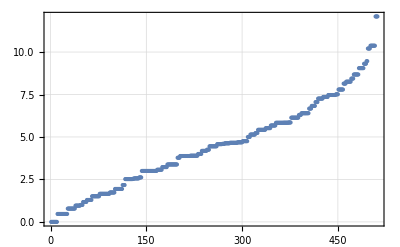

```mathematica
ListPlot[eigenval,PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
iprs=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

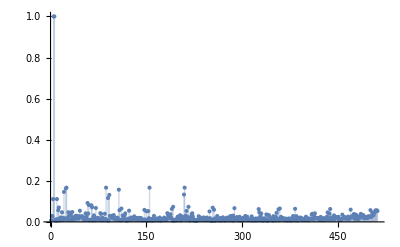

```mathematica
ListPlot[iprs,PlotRange->All,Filling->Axis]
```

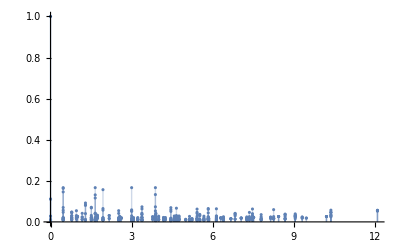

```mathematica
ListPlot[Transpose[{eigenval,iprs}],PlotRange->All,Filling->Axis]
```

## SP(t)

```mathematica
L=5;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=2;
caometer=Table[haar[1],{i,ale}];
ψTc=RandomChainProductState[L-1];
```

```mathematica
ψc=ParallelTable[Flatten[KroneckerProduct[i,ψTc]],{i,caometer}];
```

```mathematica
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
tf=10.0;
tlist=Range[0,tf,0.1];
ψct=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψc},{t,0,tf,0.1}];
```

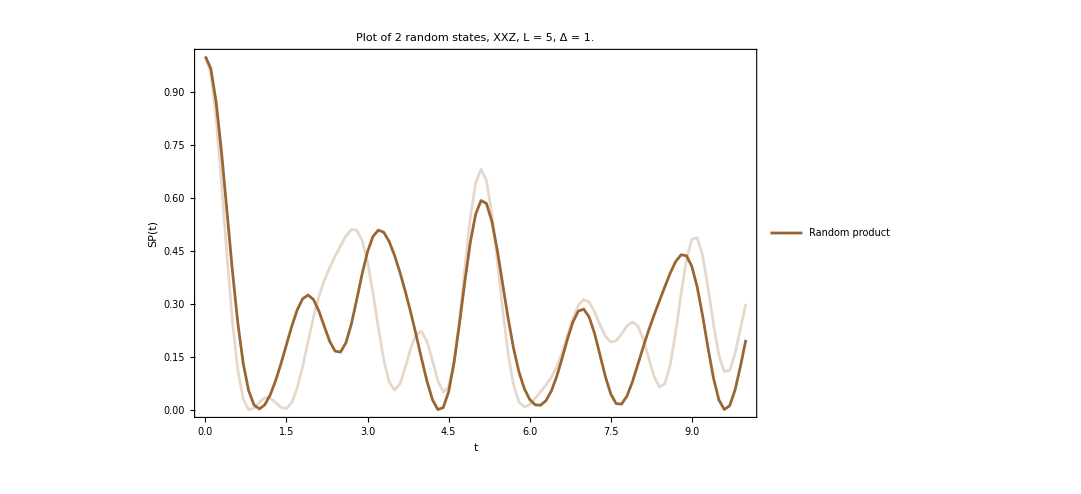

```mathematica
singlec=ListPlot[Table[{tlist[[i]],Abs[Conjugate[ψct[[j,1]]].ψct[[j,i]]]^2},{j,Length[ψct]},{i,Length[Range[0,tf,0.1]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Brown],Directive[Brown,Opacity[0.25]]},PlotRange->All,ImageSize->800,PlotLegends->{Style["Random product",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
densityc=Table[Dyad[i,i],{i,ψct}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
traceDistance[rho_,sigma_]:=1/2*Tr[MatrixPower[ConjugateTranspose[rho-sigma].(rho-sigma),1/2]];
```

```mathematica
tracedis=Table[traceDistance[i,Dyad[caometer[[1]]]],{i,reducedc}];
```

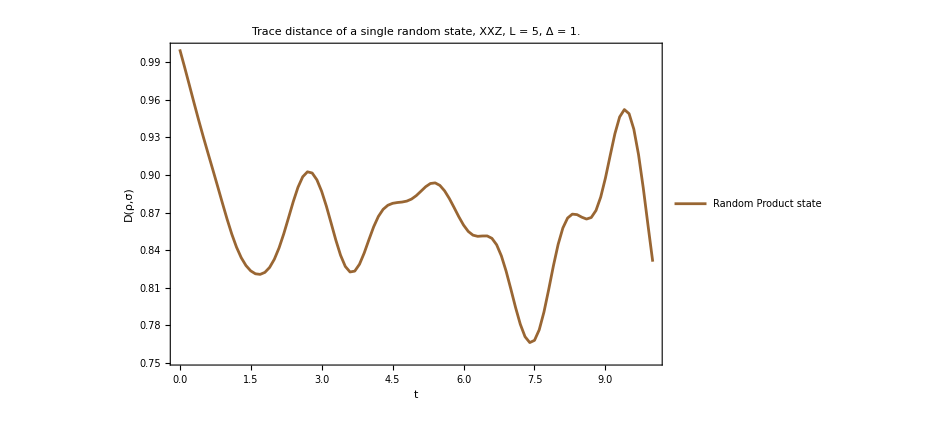

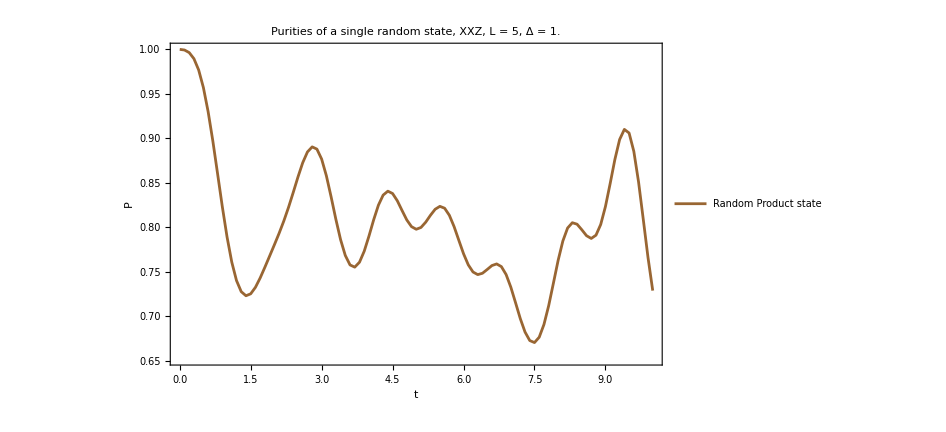

```mathematica
ListPlot[Transpose[{tlist,1-tracedis}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Trace distance of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["D(ρ,σ)"]}]

ListPlot[Transpose[{tlist,puritiesc}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

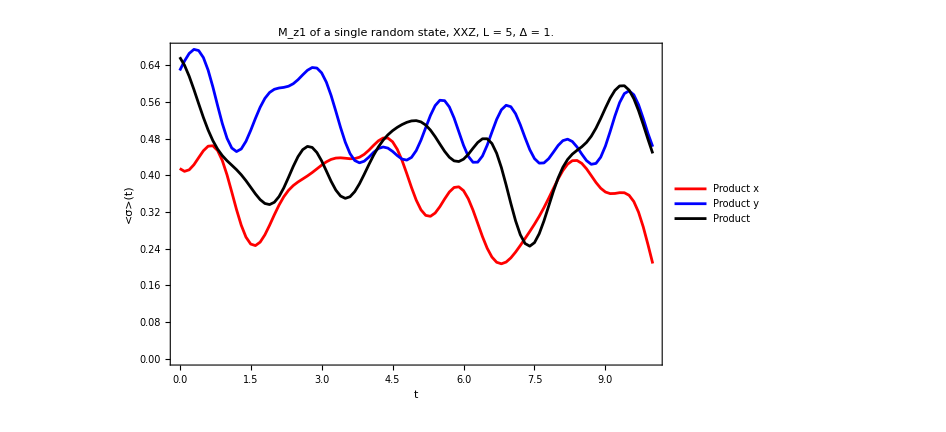

```mathematica
ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Blue,Black},PlotRange->All,ImageSize->700,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product ",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]}]
```

# Quantum channel

## Sweep XXZ various chaometer states (only random product state)

```mathematica
L=3;
(*ψe=RandomChainProductState[L-1];*)
(*ψe=coherentstate[qubit[Pi,0],L-1];*)
(*ψe=Table[coherentstate[i,L-1],{i,caometer}];*)
```

```mathematica
tf=20.;
limit=Plot[0.25,{x,0,50.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
ale=50;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
Δ=1;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
hx=J=1.;
hz=4.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ψe=Table[haar[L-1],{i,caometer}];
```

```mathematica
(*QUANTUM CHANNEL*)
(*styles={Style["Random product state, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black]};*)
styles={Style["Coherent state random, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
   figs={};
listplots={};
purities={};
directionsx={};
directionsy={};
directionsz={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
choidirectionsx={};
choidirectionsy={};
choidirectionsz={};

Do[
superOp=Superoperator[t,ψe[[i]],eigenval,eigenvec,L];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,.1}];

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]
,limit}]];

AppendTo[purities,Show[{
ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]
,limit}]];
,{i,1}];
```

```mathematica
allpurities={};
Do[

(*REDUCED DYNAMICS*)
(*ψc=Flatten[KroneckerProduct[caometer[[i]],ψe]];*)
ψc=coherentstate[caometer[[i]],L];
ψct=Table[StateEvolution[t,ψc,eigenval,eigenvec],{t,0,tf,0.1}];
densityc=Table[Dyad[i,i],{i,ψct}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesc=Table[Chop[Purity[i]],{i,reducedc}];
AppendTo[allpurities,puritiesc];
,{i,Length[caometer]}];
```

$Aborted

```mathematica
tlist=Range[0,tf,0.1];
puritiesplot=ListPlot[Table[Transpose[{tlist,Chop[i]}],{i,allpurities}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->Directive[Brown,Opacity[0.05]],PlotRange->All,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]},ImageSize->950];
puritymeanplot=ListPlot[Transpose[{tlist,Mean[allpurities]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->Directive[Brown,Opacity[1]],PlotRange->All,PlotLegends->{Style["Random Product state",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]},ImageSize->950];
purityplot=Show[{puritymeanplot,puritiesplot},PlotRange->{All,{0.48,1.01}}];
```

```mathematica
testimage=Grid[{{listplots,purities,purityplot}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
(*Export["testframe_coherent0_XXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>"_caometer.png",testimage];*)
Export["testframe_wisniacki_coherent_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_caometer.png",testimage];
```

```mathematica
testimage=Grid[{listplots,purities},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
(*Export["testframe_coherent0_XXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>"_caometer.png",testimage];*)
Export["testframe_wisniacki_haar_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_caometer.png",testimage];
```

## Spectrum ϵ

```mathematica
L=7;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
L=7;
hx=J=1.;
hz=4.;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ψe=Table[RandomChainProductState[L-1],{i,caometer}];
data1={};
data2={};
data3={};
Do[
superOp=Superoperator[t,ψe[[1]],eigenval,eigenvec,L];
(*AppendTo[choiEigenvalues,Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];*)
AppendTo[data1,Transpose[Sort[Transpose[Eigensystem[superOp]]]]];
,{t,0,tf,.1}];
```

```mathematica
eigenvalues=Table[data1[[i,1]],{i,Length[data1]}];
eigenvectors=Table[data1[[i,2]],{i,Length[data1]}];
```

{4.,3.20129,1.48173,0.353068,0.666085,1.86735,2.77142,2.71757,2.01454,1.53498,1.85758,2.7095,3.21862,2.70213,1.33383,0.19736,0.431156,1.99428,3.54856,3.81495,2.77576,1.43893,0.81764,1.20908,2.05691,2.46225,2.04138,1.31123,1.18799,2.063,3.27503,3.59055,2.48701,0.837795,0.0434605,0.664807,2.10573,3.28696,3.41185,2.52282,1.51543,1.31585,1.9591,2.59079,2.38136,1.42524,0.738959,1.21687,2.59799,3.70264,3.61597,2.40921,0.935688,0.25066,0.865142,2.19728,3.04136,2.7688,1.89824,1.45227,1.88854,2.65011,2.76275,1.91467,0.805569,0.420668,1.16525,2.60844,3.7217,3.57224,2.24816,0.917115,0.67119,1.48205,2.40665,2.5974,2.05361,1.53573,1.73364,2.54204,3.2007,3.00996,1.90552,0.624925,0.274928,1.28511,2.81934,3.57819,3.08346,1.96201,1.19973,1.30052,1.93688,2.32566,2.03169,1.37496,1.09503,1.67735,2.83147,3.55076,3.02503,1.59645,0.480034,0.531166,1.55843,2.68969,3.10355,2.62564,1.85544,1.57458,1.97975,2.53494,2.5155,1.73936,0.883047,0.899991,1.95479,3.1735,3.55223,2.85061,1.62878,0.777223,0.897236,1.77147,2.53884,2.55111,1.97343,1.54194,1.80755,2.54107,2.90042,2.34888,1.28769,0.622524,0.901212,1.95563,3.0504,3.34608,2.62527,1.57801,1.12212,1.5062,2.18072,2.41358,2.002,1.47908,1.53398,2.23377,2.97345,3.09196,2.39318,1.30124,0.664002,1.05645,2.13289,2.93875,2.87887,2.19236,1.58974,1.58483,2.04388,2.35228,2.09885,1.49325,1.11447,1.40202,2.28443,3.09514,3.07292,2.17874,1.1981,0.920983,1.43641,2.21038,2.59776,2.3664,1.88963,1.7328,2.06234,2.52536,2.60056,2.05826,1.26865,0.983895,1.56052,2.51801,3.05198,2.8066,2.05641,1.40685,1.34001,1.79691,2.24464,2.24297,1.85816,1.54728,1.72654,2.33788,2.79207,2.55401,1.77079}

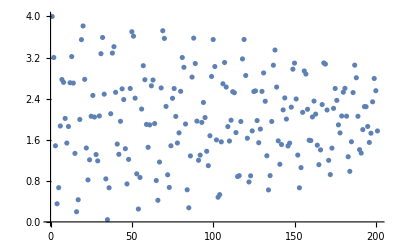

```mathematica
Table[Chop[Total[i]],{i,eigenvalues}]
ListPlot[Table[Chop[Total[i]],{i,eigenvalues}]]
```

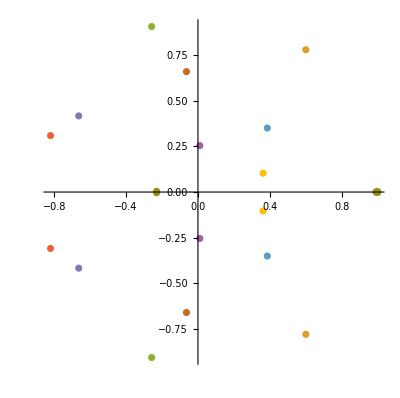

```mathematica
eigenvalues[[1;;10]]//ComplexListPlot
```

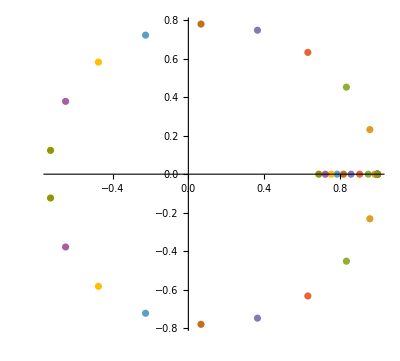

```mathematica
eigenvalues[[1;;10]]//ComplexListPlot
```

{4.,3.9057,3.62243,3.16935,2.59134,1.95395,1.3335,0.804325,0.425723,0.231915,0.227094,0.386702,0.664341,1.00235,1.34334,1.63985,1.86029,1.99037,2.03054,1.99141,1.88864,1.73929,1.55997,1.36663,1.17507,1.00094,0.858828,0.760415,0.712471,0.715479,0.763531,0.845506,0.947081,1.05291,1.14845,1.22128,1.26204,1.26534,1.23067,1.16315,1.07364,0.977597,0.892673,0.835155,0.816275,0.839422,0.899263,0.983117,1.07424,1.15597,1.21547,1.24609,1.24792,1.22667,1.19161,1.1532,1.12101,1.10216,1.10029,1.11509,1.1424,1.17503,1.20414,1.22115,1.21975,1.1974,1.15608,1.10188,1.04368,0.99119,0.952839,0.934034,0.936194,0.956675,0.989566,1.02711,1.06139,1.08588,1.09657,1.09238,1.07492,1.04769,1.01512,0.981538,0.950629,0.925171,0.907189,0.898261,0.899735,0.912718,0.937768,0.974402,1.02065,1.07284,1.12583,1.17358,1.21004,1.23018,1.23087,1.21155,1.17453,1.12485,1.06955,1.01659,0.973282,0.944832,0.933132,0.936332,0.949314,0.965034,0.97642,0.978295,0.968794,0.949843,0.926586,0.905931,0.894709,0.89799,0.918065,0.954297,1.00375,1.06223,1.12533,1.18907,1.25014,1.30578,1.35356,1.39136,1.41758,1.43156,1.43381,1.42604,1.41064,1.3899,1.36509,1.33604,1.30131,1.25904,1.20828,1.15012,1.08832,1.02901,0.979504,0.94659,0.934699,0.944661,0.97337,1.01452,1.06022,1.10301,1.13766,1.16231,1.17854,1.1904,1.20265,1.21893,1.24017,1.26412,1.2858,1.2991,1.29864,1.28156,1.24864,1.20434,1.15603,1.11246,1.08207,1.07132,1.08347,1.11783,1.16963,1.23065,1.2905,1.33857,1.36622,1.36874,1.34648,1.30473,1.25241,1.19993,1.15677,1.12962,1.12125,1.13045,1.15272,1.1816,1.21014,1.23228,1.24396,1.24385,1.23344,1.21655,1.19826,1.18348,1.17545,1.17473,1.17888,1.18315,1.18178,1.16971,1.14413}

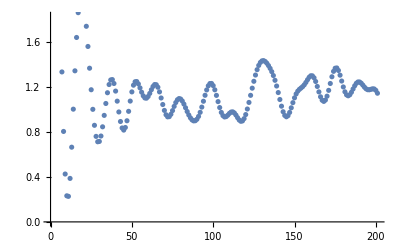

```mathematica
Table[Chop[Total[i]],{i,eigenvalues}]
ListPlot[Table[Chop[Total[i]],{i,eigenvalues}]]
```

```mathematica
plots=Table[ComplexListPlot[eigenvalues[[1;;i]],PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Gray],{i,1,50}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

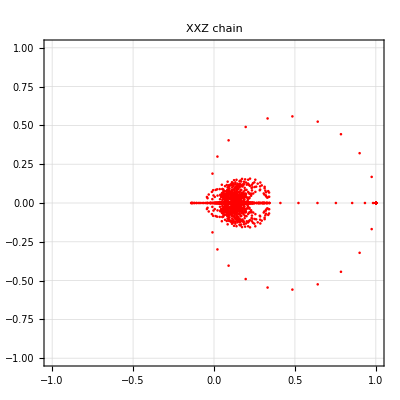

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Red,PlotLabel->Style["XXZ chain",25,Black]]
```

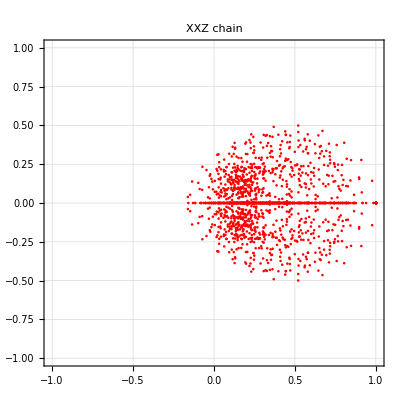

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Red,PlotLabel->Style["XXZ chain",25,Black]]
```

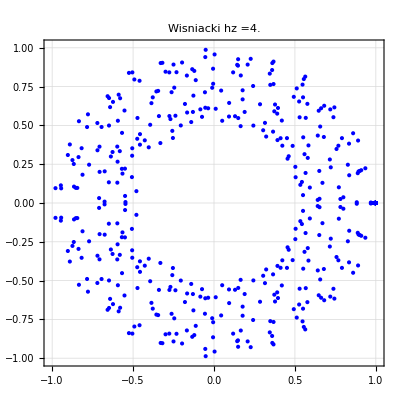

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Blue,PlotLabel->Style["Wisniacki hz ="<>ToString[hz],25,Black]]
```

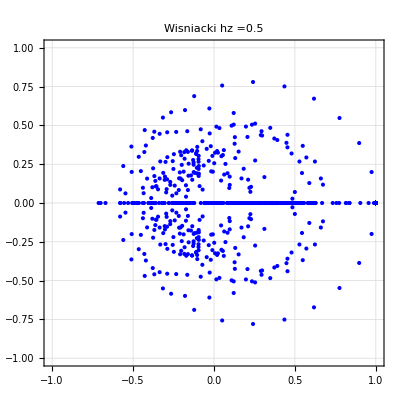

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Blue,PlotLabel->Style["Wisniacki hz ="<>ToString[hz],25,Black]]
```

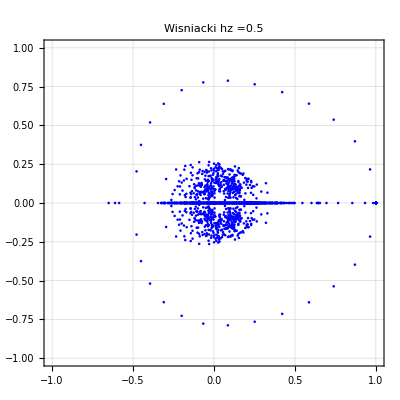

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Blue,PlotLabel->Style["Wisniacki hz ="<>ToString[hz],25,Black]]
```

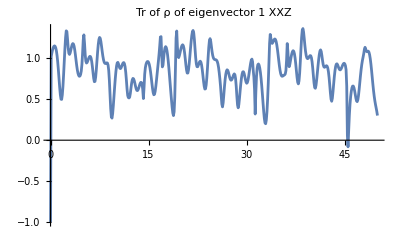

```mathematica
ρcheck=Table[Tr[bloch[rho[eigenvectors[[i,4]]]]],{i,Length[data1]}];
ListPlot[Transpose[{Range[0,50,0.1],Chop[ρcheck]}],PlotLabel->Style["Tr of ρ of eigenvector 1 XXZ", Black,18],PlotRange->All,Joined->True]
```

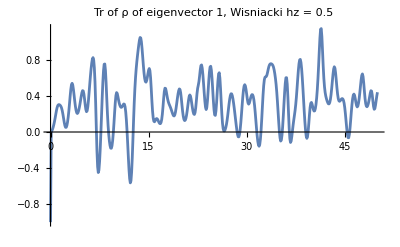

```mathematica
ρcheck=Table[Tr[bloch[rho[eigenvectors[[i,4]]]]],{i,Length[data1]}];
ListPlot[Transpose[{Range[0,50,0.1],Chop[ρcheck]}],PlotLabel->Style["Tr of ρ of eigenvector 1, Wisniacki hz = "<>ToString[hz], Black,18],PlotRange->All,Joined->True]
```

## Average over coherent states ψe

```mathematica
L=6;
tf=20.;
limit=Plot[0.25,{x,0,50.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
ale=50;
caometer=Table[haar[1],{i,ale}];
(*ψe=Table[coherentstate[i,L-1],{i,caometer}];*)
(*ψe=Table[RandomChainProductState[L-1],{i,ale}];*)
(*ψe=Table[haar[L-1],{i,caometer}];*)
```

```mathematica
Δ=1;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=100;
caometer=Table[haar[1],{i,ale}];
ψTa=Table[haar[L-1],{i,ale}];
ψTc=Table[RandomChainProductState[L-1],{i,ale}];
```

```mathematica
ψa=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTa},{i,caometer}],{ale*ale,2^L}];
ψc=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTc},{i,caometer}],{ale*ale,2^L}];
```

```mathematica
energiesa=ParallelTable[Chop[Conjugate[i].H.i],{i,ψa}];
energiesc=ParallelTable[Chop[Conjugate[i].H.i],{i,ψc}];
```

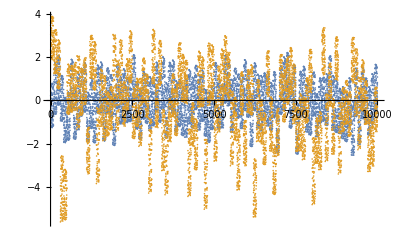

```mathematica
ListPlot[{energiesa,energiesc},PlotRange->All]
```

```mathematica
(*Find positions of elements within the range-2 to 2*)
positionsa=Position[energiesa,x_/;-2<=x<=2];
positionsc=Position[energiesc,x_/;-2<=x<=2];
```

```mathematica
ψea=Table[ψTa[[i]],{i,Flatten[positionsa]}];
ψec=Table[ψTc[[i]],{i,Flatten[positionsc]}];
```

Part::partw: Part 101 of {{0.143194+0.131395 ⅈ,-0.1679-0.049073 ⅈ,0.0490768+0.205951 ⅈ,-0.0616339-0.0514467 ⅈ,0.0182257-0.061388 ⅈ,-0.127954+0.21868 ⅈ,«21»,-0.203705+0.0263231 ⅈ,0.1919-0.0842438 ⅈ,-0.053459-0.0562309 ⅈ,0.0787842-0.0655159 ⅈ,0.00881744+0.0000331985 ⅈ},{«1»},{«1»},«46»,{«1»},«50»} does not exist.

Part::partw: Part 102 of {{0.143194+0.131395 ⅈ,-0.1679-0.049073 ⅈ,0.0490768+0.205951 ⅈ,-0.0616339-0.0514467 ⅈ,0.0182257-0.061388 ⅈ,-0.127954+0.21868 ⅈ,«21»,-0.203705+0.0263231 ⅈ,0.1919-0.0842438 ⅈ,-0.053459-0.0562309 ⅈ,0.0787842-0.0655159 ⅈ,0.00881744+0.0000331985 ⅈ},{«1»},{«1»},«46»,{«1»},«50»} does not exist.

Part::partw: Part 103 of {{0.143194+0.131395 ⅈ,-0.1679-0.049073 ⅈ,0.0490768+0.205951 ⅈ,-0.0616339-0.0514467 ⅈ,0.0182257-0.061388 ⅈ,-0.127954+0.21868 ⅈ,«21»,-0.203705+0.0263231 ⅈ,0.1919-0.0842438 ⅈ,-0.053459-0.0562309 ⅈ,0.0787842-0.0655159 ⅈ,0.00881744+0.0000331985 ⅈ},{«1»},{«1»},«46»,{«1»},«50»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 102 of {«1»} does not exist.

Part::partw: Part 105 of {«1»} does not exist.

Part::partw: Part 106 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ψea//Length
ψec//Length
```

9861

7450

```mathematica
ψe=ψTc[[1;;-1;;100]];
```

```mathematica
ψe//Length
```

75

```mathematica
(*QUANTUM CHANNEL*)
styles={Style["Coherent state random, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
allchoieigenvalues={};
allchoipurities={};

Do[

choiEigenvalues={};
choipurities={};

Do[
superOp=Superoperator[t,ψe[[i]],eigenval,eigenvec,L];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,.1}];

AppendTo[allchoieigenvalues,
Chop[choiEigenvalues]];
AppendTo[allchoipurities,Chop[choipurities]];
,{i,Length[ψe]}];
```

```mathematica
listplots={};
puritiesplots={};

Do[

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[allchoieigenvalues[[i]]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Opacity[0.15]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

AppendTo[puritiesplots,
Show[{
ListPlot[Chop[allchoipurities[[i]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Gray,Opacity[0.15]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

,{i,Length[ψe]}];
```

```mathematica
plotmeanchoieigenval=ListPlot[Transpose[Chop[Mean[allchoieigenvalues]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];

plotmeanchoipurity=ListPlot[Chop[Mean[allchoipurities]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Black,Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];
```

```mathematica
testimage=Grid[{{Show[{plotmeanchoieigenval,listplots}]},{Show[{plotmeanchoipurity,puritiesplots},PlotRange->{{0,20},All}]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
(*Export["testframe_coherent_XXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>"_caometer.png",testimage];*)
Export["testframe_wisniacki_haar_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_caometer.png",testimage];
```

```mathematica
Show[{plotmeanchoieigenval,listplots}];
Show[{plotmeanchoipurity,puritiesplots}];
```